# Mathematica Project: Exploratory Data Analysis on ‘Data Scientists’

## A big picture view of the state of data scientists and machine learning engineers.

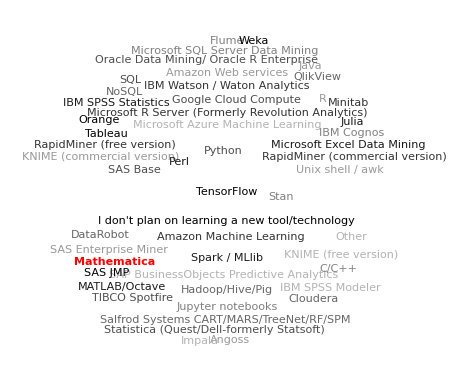

### In this Mathematica project, we will explore the capabilities of Mathematica to better understand the state of data science enthusiasts. The dataset consisting of more than 10,000 rows is obtained from Kaggle, which is a result of ‘Kaggle Survey 2017’. We will explore various capabilities of Mathematica in Data Analysis and Data Visualizations. Further, we will utilize Machine Learning techniques to train models and Classify features with several algorithms, such as k Nearest Neighbors, Random Forest.

Dataset : https : // www.kaggle.com/kaggle/kaggle - survey - 2017

```mathematica
DatasetCSV= Import["/ABHI/Workspace/Study/UCD/SEM 1/MATHEMATICA FOR RESEARCH/Project/EDA-Data-Scientists/Dataset/multipleChoiceResponses.csv"];
header=DatasetCSV[[1]];
data=DatasetCSV[[2;;]];
DataSet=Thread[header->#]&/@data//Map[Association]//Dataset;
```

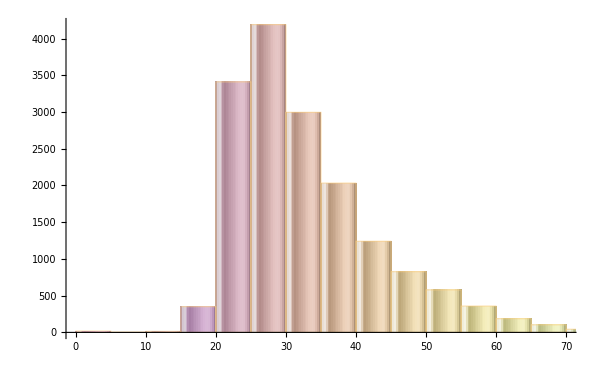

```mathematica
Histogram[DataSet[All,"Age"], 20,
ChartStyle->{"Pastel"},
ChartLabels-> Automatic,
ChartElementFunction->"GlassRectangle",
AxesLabel->Automatic,
ImageSize->{600,400}]
```

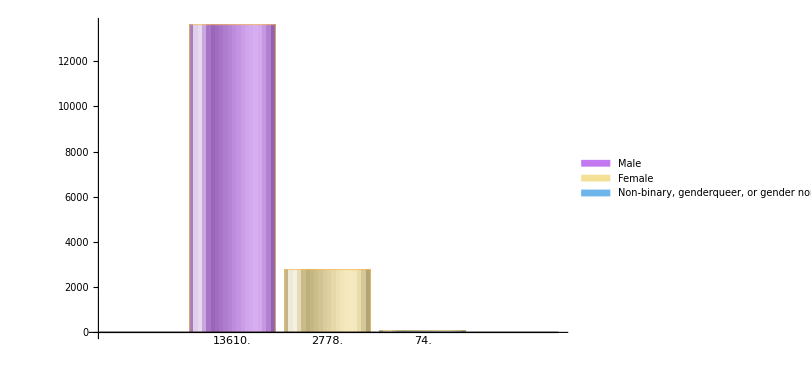

```mathematica
BarChart[Reverse[Sort[Counts[DataSet[All,"GenderSelect"]][[;;3]]]],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", ImageSize->{600,400},
ChartLegends-> Automatic,
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

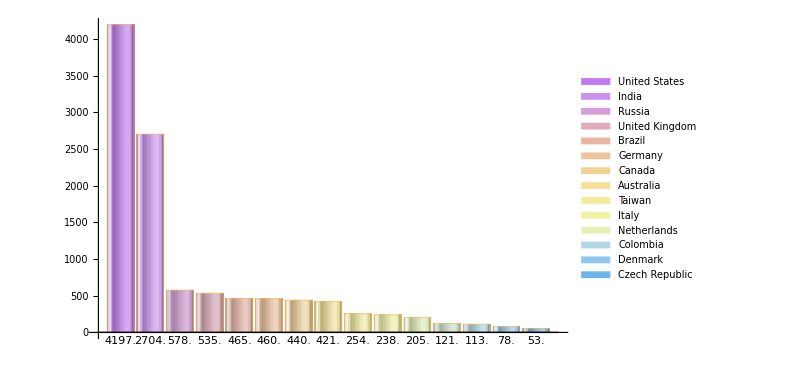

```mathematica
BarChart[Reverse[Sort[Counts[DataSet[All,"Country"]][[;;15]]]],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400},
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

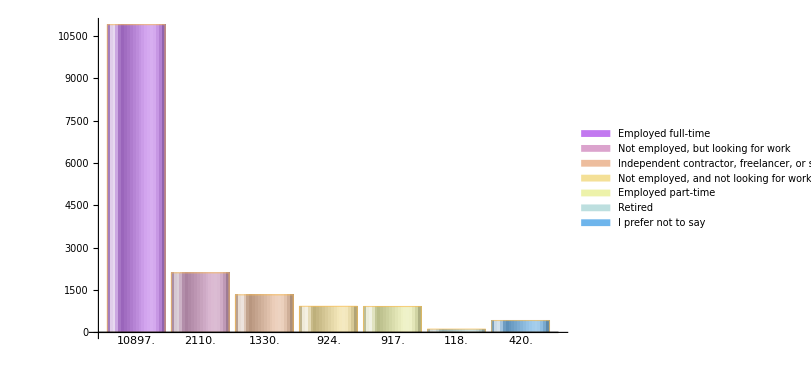

```mathematica
BarChart[Counts[DataSet[All,"EmploymentStatus"]],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

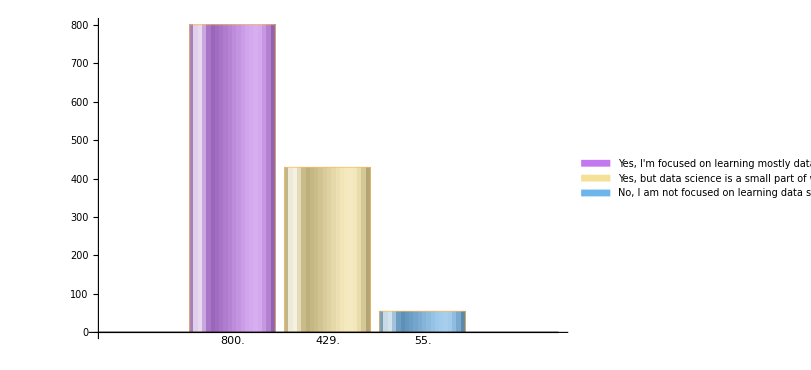

```mathematica
BarChart[Counts[RemoveEmptyElements[Normal[DataSet[All,"LearningDataScience"]]]],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

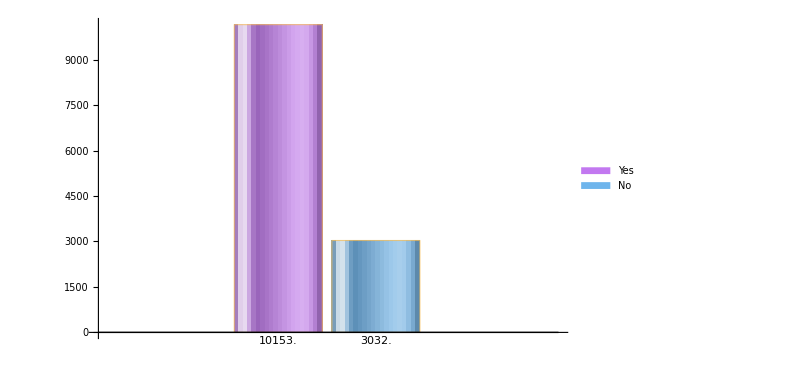

```mathematica
BarChart[Counts[RemoveEmptyElements[Normal[DataSet[All,"CodeWriter"]]]],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

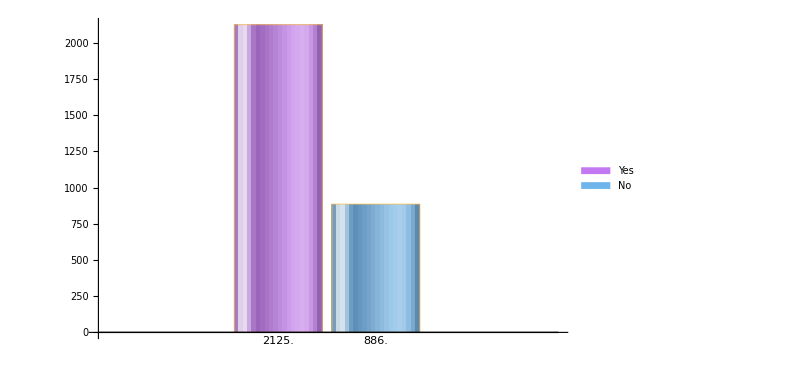

```mathematica
BarChart[Counts[RemoveEmptyElements[Normal[DataSet[All,"CareerSwitcher"]]]],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

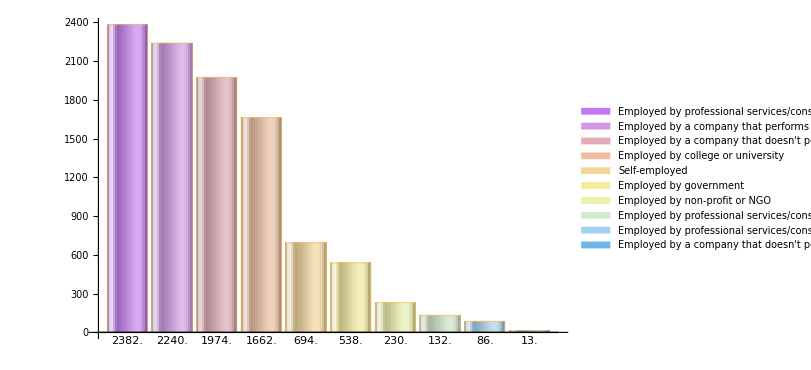

```mathematica
BarChart[Reverse[Sort[Counts[RemoveEmptyElements[Normal[DataSet[All,"CurrentEmployerType"]]]][[;;10]]]],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

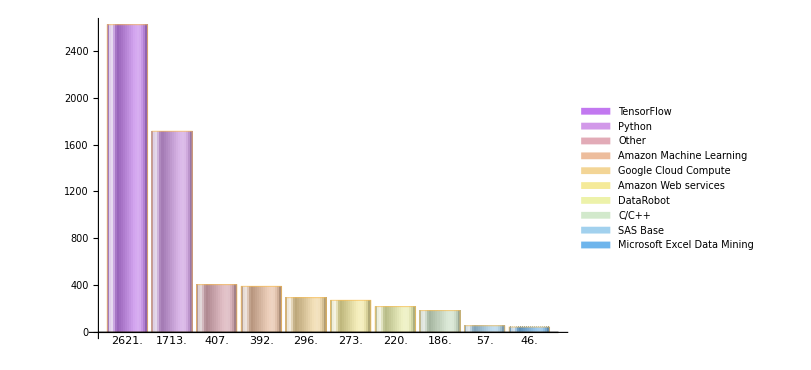

```mathematica
BarChart[Reverse[Sort[Counts[RemoveEmptyElements[Normal[DataSet[All,"MLToolNextYearSelect"]]]][[;;10]]]],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

```mathematica
RemoveEmptyElements[list_]:=
Module[{returnList= {}},
Quiet[For[i=0,i<Length[list],i++,
If[StringLength[list[[i]]]>0,
AppendTo[returnList,list[[i]]]]]];
returnList];
```

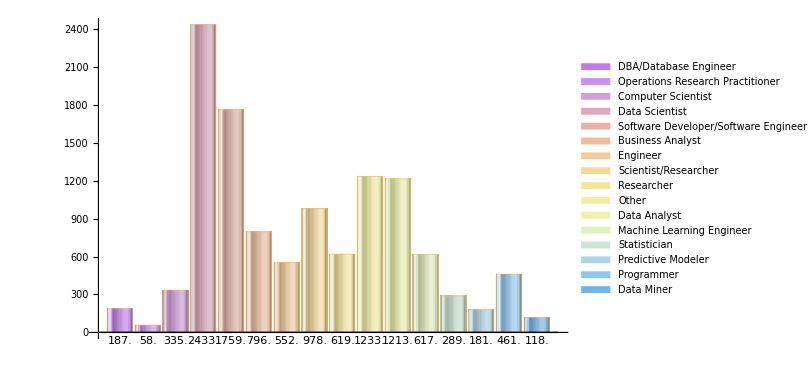

```mathematica
Jobs = RemoveEmptyElements[Normal[DataSet[All,"CurrentJobTitleSelect"]]];
BarChart[Counts[Jobs],ChartLegends-> Automatic,ChartElementFunction->"GlassRectangle",ChartStyle->"Pastel", ImageSize->{600,400}, LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

```mathematica
Languages = RemoveEmptyElements[Normal[DataSet[All,"LanguageRecommendationSelect"]]];
PieChart[Reverse[Sort[Counts[Languages]]],
ChartLegends-> Automatic,
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

-Graphics-

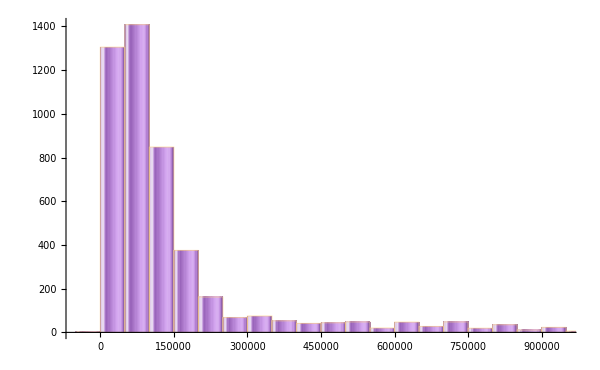

```mathematica
Histogram[DataSet[All,"CompensationAmount"], 2000000,ChartStyle->{"Pastel"},ChartLabels-> Automatic,ChartElementFunction->"GlassRectangle",AxesLabel->Automatic,ImageSize->{600,400}]
```

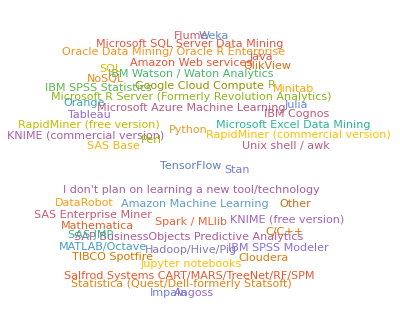

```mathematica
WordCloud[RemoveEmptyElements[Normal[DataSet[All,"MLToolNextYearSelect"]]]]
```

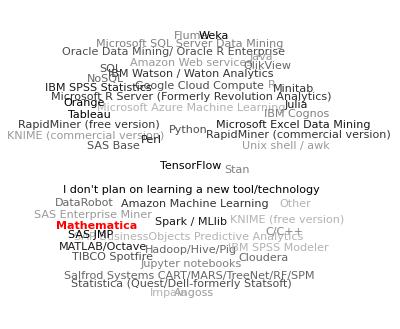

```mathematica
WordCloud[RemoveEmptyElements[Normal[DataSet[All,"MLToolNextYearSelect"]]]  /."Mathematica"->Style["Mathematica",Bold,Red], PlotTheme->"Monochrome"]
```

```mathematica
pairUp[xValues_,yValues_]:=({xValues[[#]],yValues[[#]]})&/@Range[Min[Length[xValues],Length[yValues]]];
```

```mathematica
Needs["StatisticalPlots`"]
```

```mathematica
PairwiseScatterPlot[pairUp[RemoveEmptyElements[Normal[DataSet[All,"MLToolNextYearSelect"]]],RemoveEmptyElements[Normal[DataSet[All,"LanguageRecommendationSelect"]]]]]
```

PairwiseScatterPlot[{{SAS Base,F#},{Python,Python},{Amazon Web services,R},{TensorFlow,Python},{TensorFlow,Python},{TensorFlow,Python},{TensorFlow,R},{Google Cloud Compute,SQL},{Microsoft Excel Data Mining,Python},{C/C++,Python},{Python,Python},{Other,Python},10975,{R,C/C++/C#},{Python,R},{SAS Base,R},{Python,C/C++/C#},{Microsoft Azure Machine Learning,Python},{Orange,SQL},{Julia,Python},{TensorFlow,Matlab},{KNIME (free version),R},{Python,Python},{Jupyter notebooks,Python}}]
 |  |  |  |

GEO REGION VALUE PLOT

```mathematica
CountryList = RemoveEmptyElements[DataSet[All,"Country"]];
CountryList /. "People 's Republic of China" -> "China";
For[i=0,i<Length[CountryList],i++,
Country[CountryList[[i]]] =  Count[CountryList,CountryList[[i]]]
];
CountryValueList = {};
For[i=0,i<Length[CountryList],i++, 
AppendTo[CountryValueList,Interpreter["Country"][CountryList[[i]]] -> Country[CountryList[[i]]]]
];
GeoRegionValuePlot[Union[CountryValueList],
ImageSize->{800,500},
GeoLabels->(Tooltip[#1,#2]&)]
```

-Graphics-

Graphs:

Age
Gender
Country
Employment Status
JobTitle
Language
Salary
LearningDataScience
CodeWriter
MLToolNextYearSelect
LearningPlatformSelect
CoursePlatformSelect
HardwarePersonalProjectsSelect
TimeSpentStudying
FormalEducation
MajorSelect
UniversityImportance
WorkDatasetSize
TimeGatheringDataTimeModelBuildingTimeProductionTimeVisualizingTimeFindingInsightsTimeOtherSelect
WorkDataVisualizations
CompensationAmount
CompensationCurrency
JobSatisfaction


To Do:

Intro
	what
	what all

Initial jargon

Data Manipulation
DataVisualization

Linear model
ML1
ML2

Insights
Conclusion

Write up: From kaggle
Salary convert
Salary ~ gender + age + country + Job title + Language + FormalEducation
double variable graphs